Find the head of the output from ListPlot.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Head[ListPlot[{1,2,3}]]
```

Graphics

Use @@ to compute the result of multiplying together integers up to 100.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

Use @@@ and Tuples to generate {f[a,a],f[a,b],f[b,a],f[b,b]}.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

Make a list of expression trees for the results of 4 successive applications of #^#& starting from x.

EXPECTED OUTPUT »

-Graphics- | ×

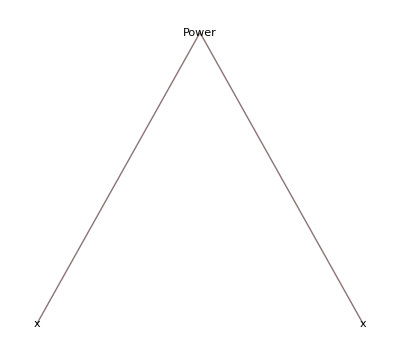
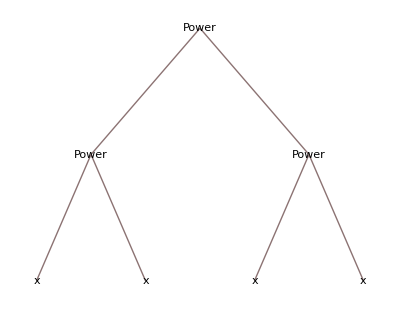
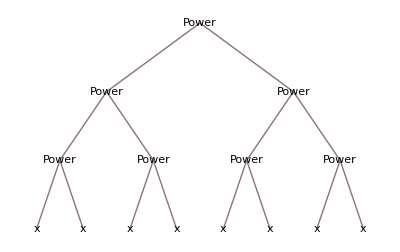
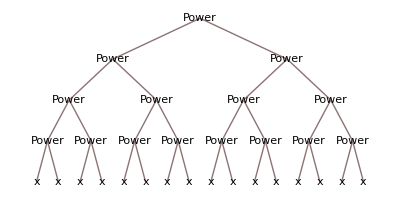
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TreeForm/@ NestList[#^#&, x, 4]
```

Find the unique cases where i^2/(j^2+1) is an integer, with i and j going up to 20.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Cases[Union[Flatten[Table[i^2/(j^2 + 1), {i, 20}, {j, 20}]]],_Integer]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

Create a graph that connects successive pairs of numbers in Table[Mod[n^2+n,100],{n,100}].

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Rule @@@ Partition[Table[Mod[n^2+n, 100], {n,100}],2,1] // Graph
```

Generate a graph showing which word can follow which in the first 200 words of the Wikipedia article on computers.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Rule@@@ Union[Partition[Take[TextWords[WikipediaData["computers"]],200],2,1]] ,VertexLabels->All]
```

Find a simpler form for f@@#&/@{{1,2},{7,2},{5,4}}.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

```mathematica
[ Click to enter code ]
```